Definition of objective function

```mathematica
obj[{x_, y_}]:= 1/(a + Cos[b(x^2+y^2)]/(1+c(x^2 + y^2)))
```

```mathematica
a = 1;
b = 1;
c = 1;


Plot3D[obj[{x,y}], {x, -Pi, Pi}, {y,-Pi, Pi},PlotRange->All]
```

-Graphics3D-

Creation of individuals in the initial population, quantisation of {x,y}, and conversion from binary to decimal

```mathematica
createIndividual:= Table[RandomInteger[1],{i,1,2},{j,1,5}]
quant = 2*Pi/31;
binCoords[bin_List]:={FromDigits[bin[[1]],2]-31/2,FromDigits[bin[[2]],2]-31/2}*quant
```

```mathematica
testind=createIndividual
Head[testind]
FromDigits[testind[[1]],2]
Join[testind[[1]][[;;-3]],testind[[1]][[4;;]]]
```

{{0,1,0,1,0},{0,0,0,1,1}}

List

10

{0,1,0,1,0}

Creation of generation 0

```mathematica
popSize=3;
```

```mathematica
initPop[n_]:=Table[createIndividual,n]
testpop = initPop[popSize]
```

{{{0,1,1,0,1},{0,1,0,1,1}},{{1,0,1,1,1},{0,0,1,0,0}},{{0,1,0,0,0},{1,0,0,1,0}}}

Selection scheme: fitness proportionate selection

```mathematica
Clear[fitProp]
```

```mathematica
fitProp[pop_List, survivorNum_]:= Module[{sortPop, totObj, sortPopC, rand, selected},

sortPop=Sort[pop, obj[binCoords[#1]]<obj[binCoords[#2]]&];
sortPop =Table[{sortPop[[n]], N[obj[binCoords[sortPop[[n]]]]]},{n,1,popSize}];
sortPopC = Table[{sortPop[[n,1]], Sum[sortPop[[k,2]],{k,n}]},{n,1,popSize}];

totObj = Sum[sortPop[[n, 2]], {n,popSize}];


selected = {};

Do[
rand =  RandomReal[{0,totObj}];
selected = Append[selected, Select[sortPopC, #[[2]]>rand&,1]  [[1,1]] ]
,survivorNum];
Return [selected]
(*sortPop = accumulate obj and divide by totobj*)
]
```

```mathematica
obj[binCoords[testpop[[1]]]]
sortTest=fitProp[testpop,3]

(*Table[{sortTest[[n]], N[obj[binCoords[sortTest[[n]]]]]},{n,1,popSize}][[1,2]]*)
```

1/(1+Cos[(106 π^2)/961]/(1+(106 π^2)/961))

{{{1,0,1,1,1},{0,0,1,0,0}},{{1,0,1,1,1},{0,0,1,0,0}},{{0,1,1,0,1},{0,1,0,1,1}}}

Crossover: single point (should inheritance completely from one parent be possible?)

```mathematica
singlePoint[{parentA_, parentB_}]:= Module[{pointX, pointY, child},
pointX = RandomInteger[{1,5}];
pointY = RandomInteger[{1,5}];

child = {Join[parentA[[1]][[;;pointX]],parentB[[1]][[pointX+1;;]]],Join[parentA[[2]][[;;pointY]],parentB[[2]][[pointY+1;;]]]};

Return[child]
]
```

```mathematica
singlePoint[{testpop[[1]],testpop[[2]]}]
```

{{0,0,1,1,1},{0,1,1,0,0}}

```mathematica
testind
{Join[testind[[1]][[;;-4]],testind[[1]][[4+1;;]]],Join[testind[[2]][[;;-5]],testind[[2]][[5+1;;]]]}
testind[[1]][[4;;]]
```

{{0,1,0,1,0},{0,0,0,1,1}}

{{0,1,0},{0}}

{1,0}

```mathematica
newPop[iter_, parents_]:=Module[{new},
new = {};
Do[
new = Append[new, Map[singlePoint,Partition[RandomSample[parents],2]]]; (*non-monogamous population*)
,iter];
Return[Flatten[new,1]]
]
```

Mutation: bit string (try using map???)

```mathematica
mutate[person_, rate_]:= Map[If[RandomReal[]*100<rate, 1-#,#]&,person,2]

(*For[i=1,i≤5,i++,If[RandomReal[]*100<rate, person[[*)
```

```mathematica
testind
mutate[testind,20]
```

{{0,1,0,1,0},{0,0,0,1,1}}

{{0,1,0,0,0},{1,1,1,0,0}}

Testing

```mathematica
averagefitness[pop_]:= Sum[obj[binCoords[pop[[n]]]],{n,1,Length[pop]}]/Length[pop]
fittestindividual[pop_]:=Sort[pop, obj[binCoords[#1]]>obj[binCoords[#2]]&][[1]]
```

Main body

-Graphics3D-

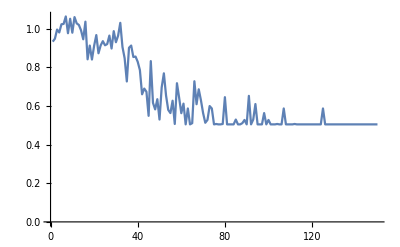

```mathematica
population = initPop[10];
iters = 150;
mutationrate = 50;
fitlist = {};
Do[ (*training*)
breeders =fitProp[population,4];
population = newPop[5,breeders];
population=Map[mutate[#,mutationrate]&, population, {1}];
(*need to cull? or adjust parameters for constant population?*)
mutationrate=mutationrate*0.95;
fitlist = Append[fitlist,averagefitness[population]];
(*Print[N[averagefitness[population]]];
Print[N[fittestindividual[population]]];*)
,iters
]
(*Print[binCoords[fittestindividual[population]]]*)

Show[Plot3D[obj[{x,y}], {x, -Pi, Pi}, {y,-Pi, Pi},PlotRange->All, ColorFunction->"Pastel"],
ListPointPlot3D[
{{binCoords[fittestindividual[population]][[1]],binCoords[fittestindividual[population]][[2]],N[obj[binCoords[fittestindividual[population]]]]}}
,PlotRange->All]
	]

ListPlot[fitlist, Joined->True]
```